```mathematica
PBC = True;
hermitian = True;

NUnit = 8;

systemLengthX = NUnit;
systemLengthY = NUnit;
systemLengthZ = 4;


p1=Flatten[Table[{{5-p,5-q,z,2},{5-p,5-q,z,1}},{z,1,systemLengthZ},{p,1,4},{q,1,4}],3];
p2=Flatten[Table[{{9-p,5-q,z,2},{9-p,5-q,z,1}},{z,1,systemLengthZ},{p,1,4},{q,1,4}],3];
p3=Flatten[Table[{{4+p,4+q,z,1},{4+p,4+q,z,2}},{z,1,systemLengthZ},{p,1,4},{q,1,4}],3];
p4=Flatten[Table[{{p,4+q,z,1},{p,4+q,z,2}},{z,1,systemLengthZ},{p,1,4},{q,1,4}],3];

coordConvention=Flatten[Table[Join[p1[[(z-1)*NUnit^2/2+1;;z*NUnit^2/2]],p2[[(z-1)*NUnit^2/2+1;;z*NUnit^2/2]],p3[[(z-1)*NUnit^2/2+1;;z*NUnit^2/2]],p4[[(z-1)*NUnit^2/2+1;;z*NUnit^2/2]]],{z,1,systemLengthZ}],1];

reorderingPos = {Flatten[Table[Position[coordConvention,{x,y,z,1}][[1,1]],{x,1,NUnit},{y,1,NUnit},{z,1,systemLengthZ}],2],Flatten[Table[Position[coordConvention,{x,y,z,2}][[1,1]],{x,1,NUnit},{y,1,NUnit},{z,1,systemLengthZ}],2]};
```

```mathematica
coordConvention//MatrixForm;
```

```mathematica
appliedVoltage = 1;
RShunt = 50;

frequency = 2.5*10^6;

L1Value = 27*10^-6;
L2Value = 5.6*10^-6;
L3Value = 27*10^-6;

C1Value = 150*10^-12;
C2Value = 75*10^-12;
C3Value = 150*10^-12;

Ry = 15.92;


inputRow =4;
inputColumn = 4;
inputHeight = 1;

InputNodes ={{inputRow,inputColumn,inputHeight,1},{inputRow,inputColumn,inputHeight,2}};

inputPos ={Position[coordConvention,{inputRow,inputColumn,1,1}][[1,1]],Position[coordConvention,{inputRow,inputColumn,1,2}][[1,1]]};
```

```mathematica
coordConvention//Dimensions
coordConvention[[1]]
```

{512,4}

{4,4,1,2}

```mathematica
PBC ==False
```

False

```mathematica
Manipulate[{totalNodeConductanceMatrixFourier[[x,x]],coordConvention[[x]]},{x,1,8*8*4*2,1},{y,1,8*8*4*2,1}]
```

Part::partd: Part specification totalNodeConductanceMatrixFourier⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification coordConvention⟦1⟧ is longer than depth of object.

Part::partd: Part specification totalNodeConductanceMatrixFourier⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification coordConvention⟦1⟧ is longer than depth of object.

Part::partd: Part specification totalNodeConductanceMatrixFourier⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification coordConvention⟦1⟧ is longer than depth of object.

Part::partd: Part specification totalNodeConductanceMatrixFourier⟦1,1⟧ is longer than depth of object.

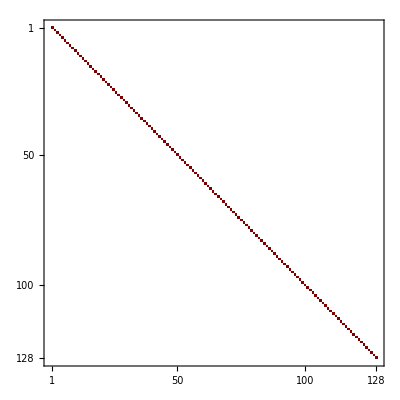

```mathematica
totalNodeConductanceMatrixFourier//MatrixPlot
```

```mathematica
coordConvention//Dimensions
Position[totalNodeConductanceMatrixFourier,2*I*driveFreq*C3Value+2*I*driveFreq*C2Value]//Dimensions
```

{512,4}

{64,3}

```mathematica
circuitGroundMatrixFourier = Table[Which[x==y,Which[coordConvention[[x,4]]==1,(I*driveFreq*L2Value)^-1+If[PBC==False,If[coordConvention[[x,3]]==1 ||coordConvention[[x,3]]==systemLengthZ,I*driveFreq*C1Value,0],0],
coordConvention[[x,4]]==2,(I*driveFreq*L3Value)^-1+If[PBC==False,If[coordConvention[[x,3]]==1 ||coordConvention[[x,3]]==systemLengthZ,I*driveFreq*C1Value,0],0],True,0],True,0],{x,1,Length[coordConvention]},{y,1,Length[coordConvention]}];

adjacencyMatrixXToYSameCellFourier= Table[Which[
coordConvention[[x]]==coordConvention[[y]]-{0,0,0,1}||
coordConvention[[x]]==coordConvention[[y]]+{0,0,0,1},I*driveFreq*C1Value,
True,0],{x,1,Length[coordConvention]},{y,1,Length[coordConvention]}];
 
adjacencyMatrixXToYDifferentCellFourier = Table[Which[
coordConvention[[x]]==Mod[coordConvention[[y]]+{-1,1,0,1},8,1] ||
coordConvention[[x]]==Mod[coordConvention[[y]]-{-1,1,0,1},8,1] ||
coordConvention[[x]]==Mod[coordConvention[[y]]+{1,-1,0,1},8,1]||
coordConvention[[x]]==Mod[coordConvention[[y]]-{1,-1,0,1},8,1] ,I*driveFreq*C2Value,
True,0],{x,1,Length[coordConvention]},{y,1,Length[coordConvention]}];

adjacencyMatrixXToXFourier = Table[Which[
coordConvention[[x]]==Mod[coordConvention[[y]]+{0,1,0,0},8,1] ||
coordConvention[[x]]==Mod[coordConvention[[y]]-{0,1,0,0} ,8,1]
,Which[
coordConvention[[x,4]]==1,I*driveFreq*C3Value,
coordConvention[[x,4]]==2,(I*driveFreq*L1Value)^-1,
coordConvention[[x]]==Mod[coordConvention[[y]]+{1,0,0,0},8,1] ||
coordConvention[[x]]==Mod[coordConvention[[y]]-{1,0,0,0} ,8,1]
,If[hermitian==False,Ry^-1,0],
True,0],True,0],{x,1,Length[coordConvention]},{y,1,Length[coordConvention]}];

adjacencyMatrixZ=
Table[Which[PBC==True,
Which[coordConvention[[x]]==Join[coordConvention[[y]][[;;2]] , {Mod[ coordConvention[[y]][[3]]+1, systemLengthZ, 1]},{Mod[coordConvention[[y]][[4]]+1,2,1]}]||coordConvention[[x]]==Join[coordConvention[[y]][[;;2]] , {Mod[ coordConvention[[y]][[3]]-1, systemLengthZ, 1]},{Mod[coordConvention[[y]][[4]]+1,2,1]}]
,I*driveFreq*C1Value,True,0],
PBC==False,
Which[
!coordConvention[[x,3]]==1 &&!coordConvention[[y,3]]==systemLengthZ &&!coordConvention[[y,3]]==1 &&!coordConvention[[x,3]]==systemLengthZ,
Which[coordConvention[[x]]==coordConvention[[y]] + {0, 0, 1, -1} ||coordConvention[[x]]==coordConvention[[y]] + {0, 0, 1, 1} ||coordConvention[[x]]==coordConvention[[y]] - {0, 0, 1, -1}||coordConvention[[x]]==coordConvention[[y]] - {0, 0, 1, 1} ,I*driveFreq*C1Value,
True,0]
,
coordConvention[[x,3]]==1 &&!coordConvention[[y,3]]==systemLengthZ ||coordConvention[[y,3]]==1 &&!coordConvention[[x,3]]==systemLengthZ,Which[coordConvention[[x]]==coordConvention[[y]] - {0, 0, 1, -1} ||coordConvention[[x]]==coordConvention[[y]] - {0, 0, 1, 1}||coordConvention[[x]]==coordConvention[[y]] + {0, 0, 1, -1} ||coordConvention[[x]]==coordConvention[[y]] + {0, 0, 1, 1} ,I*driveFreq*C1Value,True,0]
,
coordConvention[[x,3]]==systemLengthZ &&!coordConvention[[y,3]]==1||coordConvention[[y,3]]==systemLengthZ &&!coordConvention[[x,3]]==1

,Which[coordConvention[[x]]==coordConvention[[y]] - {0, 0, 1, -1} ||coordConvention[[x]]==coordConvention[[y]] - {0, 0, 1, 1}||coordConvention[[x]]==coordConvention[[y]] + {0, 0, 1, -1} ||coordConvention[[x]]==coordConvention[[y]] + {0, 0, 1, 1} ,I*driveFreq*C1Value,True,0]
,True,0],

True,

0]
  , {x, 1, Length[coordConvention]}, {y, 1, Length[coordConvention]}];

totalNodeConductanceMatrixFourier = Table[
Which[x==y,
Which[coordConvention[[x,4]]==1,
2*I*driveFreq*C3Value+2*I*driveFreq*C2Value+If[hermitian==False,2 Ry^-1,0]+Which[PBC==True,2*I*driveFreq*C1Value,PBC==False,If[coordConvention[[x,3]]==1 ||coordConvention[[x,3]]==systemLengthZ,I*driveFreq*C1Value,2*I*driveFreq*C1Value],True,0],

coordConvention[[x,4]]==2,2*I*driveFreq*C2Value+2*(I*driveFreq*L1Value)^-1+If[hermitian==False,2 Ry^-1,0]+
Which[PBC==True,2*I*driveFreq*C1Value,PBC==False,If[coordConvention[[x,3]]==1 ||coordConvention[[x,3]]==systemLengthZ,I*driveFreq*C1Value,2*I*driveFreq*C1Value],True,0]
,True,0],True,0],{x,1,Length[coordConvention]},{y,1,Length[coordConvention]}];
```

```mathematica
testLap = totalNodeConductanceMatrixFourier-(adjacencyMatrixXToXFourier+adjacencyMatrixXToYDifferentCellFourier+adjacencyMatrixXToYSameCellFourier+adjacencyMatrixZ)+circuitGroundMatrixFourier;
```

```mathematica
testLap//MatrixPlot
```

-Graphics-

```mathematica
jMatrix[x,y,z]
```

jMatrix[x,y,z]

```mathematica
x=1;
y=1;
z =1;
sub = 1;

x2 = 1;
y2 = 1;
z2 = 2;
sub2 = 2;


coordConvention[[Position[coordConvention,{x,y,z,sub}][[1,1]]]]
coordConvention[[Position[coordConvention,{x2,y2,z2,sub2}][[1,1]]]]

testLap[[Position[coordConvention,{x,y,z,sub}][[1,1]],Position[coordConvention,{x2,y2,z2,sub2}][[1,1]]]]



Clear[x,y,z,sub,x2,y2,z2,sub2]
```

{1,1,1,1}

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

{{4,4,1,2},{4,4,1,1},{4,3,1,2},{4,3,1,1},{4,2,1,2},{4,2,1,1},{4,1,1,2},{4,1,1,1},{3,4,1,2},{3,4,1,1},{3,3,1,2},{3,3,1,1},{3,2,1,2},{3,2,1,1},{3,1,1,2},{3,1,1,1},{2,4,1,2},{2,4,1,1},{2,3,1,2},{2,3,1,1},{2,2,1,2},{2,2,1,1},{2,1,1,2},{2,1,1,1},{1,4,1,2},{1,4,1,1},{1,3,1,2},{1,3,1,1},{1,2,1,2},{1,2,1,1},{1,1,1,2},{1,1,1,1},{8,4,1,2},{8,4,1,1},{8,3,1,2},{8,3,1,1},{8,2,1,2},{8,2,1,1},{8,1,1,2},{8,1,1,1},{7,4,1,2},{7,4,1,1},{7,3,1,2},{7,3,1,1},{7,2,1,2},{7,2,1,1},{7,1,1,2},{7,1,1,1},{6,4,1,2},{6,4,1,1},{6,3,1,2},{6,3,1,1},{6,2,1,2},{6,2,1,1},{6,1,1,2},{6,1,1,1},{5,4,1,2},{5,4,1,1},{5,3,1,2},{5,3,1,1},{5,2,1,2},{5,2,1,1},{5,1,1,2},{5,1,1,1},{5,5,1,1},{5,5,1,2},{5,6,1,1},{5,6,1,2},{5,7,1,1},{5,7,1,2},{5,8,1,1},{5,8,1,2},{6,5,1,1},{6,5,1,2},{6,6,1,1},{6,6,1,2},{6,7,1,1},{6,7,1,2},{6,8,1,1},{6,8,1,2},{7,5,1,1},{7,5,1,2},{7,6,1,1},{7,6,1,2},{7,7,1,1},{7,7,1,2},{7,8,1,1},{7,8,1,2},{8,5,1,1},{8,5,1,2},{8,6,1,1},{8,6,1,2},{8,7,1,1},{8,7,1,2},{8,8,1,1},{8,8,1,2},{1,5,1,1},{1,5,1,2},{1,6,1,1},{1,6,1,2},{1,7,1,1},{1,7,1,2},{1,8,1,1},{1,8,1,2},{2,5,1,1},{2,5,1,2},{2,6,1,1},{2,6,1,2},{2,7,1,1},{2,7,1,2},{2,8,1,1},{2,8,1,2},{3,5,1,1},{3,5,1,2},{3,6,1,1},{3,6,1,2},{3,7,1,1},{3,7,1,2},{3,8,1,1},{3,8,1,2},{4,5,1,1},{4,5,1,2},{4,6,1,1},{4,6,1,2},{4,7,1,1},{4,7,1,2},{4,8,1,1},{4,8,1,2}}⟦{}⟦1,1⟧⟧

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

{{-(1000000 ⅈ)/(9 driveFreq)+(9 ⅈ driveFreq)/20000000000,-(3 ⅈ driveFreq)/10000000000,(1000000 ⅈ)/(27 driveFreq),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(3 ⅈ driveFreq)/40000000000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(3 ⅈ driveFreq)/40000000000,0,0,0,0,0,0,0,0,(1000000 ⅈ)/(27 driveFreq),0,0,0,0,0,0},{1},124,{1},{0,0,125,-(1000000 ⅈ)/(9 driveFreq)+(9 ⅈ driveFreq)/20000000000}}⟦32,1⟧
 |  |  |  |

```mathematica
testLapPBC-testLapOBC//MatrixPlot
```

MatrixPlot::mat0: Argument -testLapOBC+testLapPBC at position 1 is not a matrix.

MatrixPlot[-testLapOBC+testLapPBC]

```mathematica
------------
```

```mathematica
laplacianMatrixFourier[ω_]:= ReplaceAll[totalNodeConductanceMatrixFourier-(adjacencyMatrixXToXFourier+adjacencyMatrixXToYDifferentCellFourier+adjacencyMatrixXToYSameCellFourier+adjacencyMatrixZ)+circuitGroundMatrixFourier,driveFreq-> 2π*ω];

inverseLaplacianMatrixFourier[ω_]:= Inverse[laplacianMatrixFourier[ω]];

inverseLaplacianMatrixFourierFreq = inverseLaplacianMatrixFourier[frequency];

currentVectorCosSubA = Table[If[coordConvention[[node]]==InputNodes[[1]],appliedVoltage/(RShunt+inverseLaplacianMatrixFourierFreq[[inputPos[[1]],inputPos[[1]]]]),0],{node, 1,Length[coordConvention]}];

currentVectorCosSubB = Table[If[coordConvention[[node]]==InputNodes[[2]],appliedVoltage/(RShunt+inverseLaplacianMatrixFourierFreq[[inputPos[[2]],inputPos[[2]]]]),0],{node, 1,Length[coordConvention]}];
```

```mathematica
inverseLaplacianMatrixFourierFreq//Dimensions
coordConvention//Dimensions
```

{128,128}

{128,4}

```mathematica
currentVectorDynamic = Table[Which[coordConvention[[node]]=={3,3,1,2},Exp[-I*0],
coordConvention[[node]]=={2,3,1,2},Exp[-I*π/2],True,0],{node, 1,Length[coordConvention]}];
```

```mathematica
currentVectorDynamic//MatrixForm;
```

```mathematica
dynamicVoltages =Dot[currentVectorDynamic,inverseLaplacianMatrixFourierFreq];
```

```mathematica
dynamicVoltages//Dimensions
```

{128}

```mathematica
voltagesDynamicSimulatedOrdered = Table[dynamicVoltages[[reorderingPos[[sub,node]]]],{sub,1,2},{node,1,systemLengthZ*NUnit^2}];
voltagesDynamicSimulatedCartesian = Table[voltagesDynamicSimulatedOrdered[[sub,((x-1)*NUnit*systemLengthZ)+((y-1)*systemLengthZ)+z]],{sub,1,2},{x,1,NUnit},{y,1,NUnit},{z,1,systemLengthZ}];
```

```mathematica
voltagesDynamicSimulatedOrdered//Dimensions
voltagesDynamicSimulatedCartesian//Dimensions
```

{2,64}

{2,8,8,1}

```mathematica
voltageVectorCos = {Dot[currentVectorCosSubA,inverseLaplacianMatrixFourierFreq],Dot[currentVectorCosSubB,inverseLaplacianMatrixFourierFreq]};
```

```mathematica
voltageVectorCos//Dimensions
```

{2,128}

```mathematica
j = 8;
l = 8;
k=2;

coordConvention[[reorderingPos[[1,((j-1)*NUnit*systemLengthZ)+((l-1)*systemLengthZ)+k]]]]
Clear[j,k,l]
reorderingPos[[1]][[;;20]]
coordConvention[[reorderingPos[[1]]]][[;;20]]
```

Part::partw: Part 65 of {32,30,28,26,97,99,101,103,24,22,«54»} does not exist.

Part::pkspec1: The expression {{32,30,28,26,97,99,101,103,24,22,«54»},{31,29,27,25,98,100,102,104,23,21,«54»}}⟦1,65⟧ cannot be used as a part specification.

{{4,4,1,2},{4,4,1,1},{4,3,1,2},{4,3,1,1},{4,2,1,2},{4,2,1,1},{4,1,1,2},{4,1,1,1},{3,4,1,2},{3,4,1,1},{3,3,1,2},{3,3,1,1},{3,2,1,2},{3,2,1,1},{3,1,1,2},{3,1,1,1},{2,4,1,2},{2,4,1,1},{2,3,1,2},{2,3,1,1},{2,2,1,2},{2,2,1,1},{2,1,1,2},{2,1,1,1},{1,4,1,2},{1,4,1,1},{1,3,1,2},{1,3,1,1},{1,2,1,2},{1,2,1,1},{1,1,1,2},{1,1,1,1},{8,4,1,2},{8,4,1,1},{8,3,1,2},{8,3,1,1},{8,2,1,2},{8,2,1,1},{8,1,1,2},{8,1,1,1},{7,4,1,2},{7,4,1,1},{7,3,1,2},{7,3,1,1},{7,2,1,2},{7,2,1,1},{7,1,1,2},{7,1,1,1},{6,4,1,2},{6,4,1,1},{6,3,1,2},{6,3,1,1},{6,2,1,2},{6,2,1,1},{6,1,1,2},{6,1,1,1},{5,4,1,2},{5,4,1,1},{5,3,1,2},{5,3,1,1},{5,2,1,2},{5,2,1,1},{5,1,1,2},{5,1,1,1},{5,5,1,1},{5,5,1,2},{5,6,1,1},{5,6,1,2},{5,7,1,1},{5,7,1,2},{5,8,1,1},{5,8,1,2},{6,5,1,1},{6,5,1,2},{6,6,1,1},{6,6,1,2},{6,7,1,1},{6,7,1,2},{6,8,1,1},{6,8,1,2},{7,5,1,1},{7,5,1,2},{7,6,1,1},{7,6,1,2},{7,7,1,1},{7,7,1,2},{7,8,1,1},{7,8,1,2},{8,5,1,1},{8,5,1,2},{8,6,1,1},{8,6,1,2},{8,7,1,1},{8,7,1,2},{8,8,1,1},{8,8,1,2},{1,5,1,1},{1,5,1,2},{1,6,1,1},{1,6,1,2},{1,7,1,1},{1,7,1,2},{1,8,1,1},{1,8,1,2},{2,5,1,1},{2,5,1,2},{2,6,1,1},{2,6,1,2},{2,7,1,1},{2,7,1,2},{2,8,1,1},{2,8,1,2},{3,5,1,1},{3,5,1,2},{3,6,1,1},{3,6,1,2},{3,7,1,1},{3,7,1,2},{3,8,1,1},{3,8,1,2},{4,5,1,1},{4,5,1,2},{4,6,1,1},{4,6,1,2},{4,7,1,1},{4,7,1,2},{4,8,1,1},{4,8,1,2}}⟦{{32,30,28,26,97,99,101,103,24,22,20,18,105,107,109,111,16,14,12,10,113,115,117,119,8,6,4,2,121,123,125,127,64,62,60,58,65,67,69,71,56,54,52,50,73,75,77,79,48,46,44,42,81,83,85,87,40,38,36,34,89,91,93,95},{31,29,27,25,98,100,102,104,23,21,19,17,106,108,110,112,15,13,11,9,114,116,118,120,7,5,3,1,122,124,126,128,63,61,59,57,66,68,70,72,55,53,51,49,74,76,78,80,47,45,43,41,82,84,86,88,39,37,35,33,90,92,94,96}}⟦1,65⟧⟧

{32,30,28,26,97,99,101,103,24,22,20,18,105,107,109,111,16,14,12,10}

{{1,1,1,1},{1,2,1,1},{1,3,1,1},{1,4,1,1},{1,5,1,1},{1,6,1,1},{1,7,1,1},{1,8,1,1},{2,1,1,1},{2,2,1,1},{2,3,1,1},{2,4,1,1},{2,5,1,1},{2,6,1,1},{2,7,1,1},{2,8,1,1},{3,1,1,1},{3,2,1,1},{3,3,1,1},{3,4,1,1}}

```mathematica
x=1;
y=1;
z=4;

Position[coordConvention,{x,y,z,1}][[1,1]]
reorderingPos//Dimensions

Clear[x,y,z]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1,1⟧

{2,64}

```mathematica
voltagesSimulatedOrdered = Table[voltageVectorCos[[subInput,reorderingPos[[sub,node]]]],{subInput,1,2},{sub,1,2},{node,1,systemLengthZ*NUnit^2}];

currentVectorSimulatedOrdered =Table[If[reorderingPos[[sub,node]]==inputPos[[sub]],appliedVoltage/(50+inverseLaplacianMatrixFourierFreq[[inputPos[[sub]],inputPos[[sub]]]]),0],{sub,1,2},{node,1,systemLengthZ*NUnit^2}];
```

```mathematica
fourierVoltagesV1 = Table[∑_(k=1)^systemLengthZ (∑_(l=1)^NUnit ( ∑_(j=1)^NUnit voltagesSimulatedOrdered[[subInput,sub,((j-1)*NUnit*systemLengthZ)+((l-1)*systemLengthZ)+k]]*Exp[-ⅈ*2*π*kx*(j)/NUnit])*Exp[-ⅈ*2*π*ky*(l)/NUnit])*Exp[-ⅈ*2*π*kz*(k)/systemLengthZ],{subInput,1,2},{sub,1,2},{kx,1,NUnit},{ky,1,NUnit},{kz,1,systemLengthZ}];

fourierCurrentVector = Table[∑_(k=1)^systemLengthZ (∑_(l=1)^NUnit ( ∑_(j=1)^NUnit currentVectorSimulatedOrdered[[sub,((j-1)*NUnit*systemLengthZ)+((l-1)*systemLengthZ)+k]]*Exp[-ⅈ*2*π*kx*(j)/NUnit])*Exp[-ⅈ*2*π*ky*(l)/NUnit])*Exp[-ⅈ*2*π*kz*(k)/systemLengthZ],{sub,1,2},{kx,1,NUnit},{ky,1,NUnit},{kz,1,systemLengthZ}];
```

```mathematica
Detk=Table[ (fourierVoltagesV1[[1,1,kx,ky,kz]]*fourierVoltagesV1[[2,2,kx,ky,kz]])/(fourierCurrentVector[[1,kx,ky,kz]]*fourierCurrentVector[[2,kx,ky,kz]])-(fourierVoltagesV1[[1,2,kx,ky,kz]]*fourierVoltagesV1[[2,1,kx,ky,kz]])/(fourierCurrentVector[[1,kx,ky,kz]]*fourierCurrentVector[[2,kx,ky,kz]]),{kx,1,NUnit},{ky,1,NUnit},{kz,1,systemLengthZ}];

Lap = Table[1/Detk[[kx,ky,kz]]*{{fourierVoltagesV1[[2,2,kx,ky,kz]]/fourierCurrentVector[[2,kx,ky,kz]],-fourierVoltagesV1[[2,1,kx,ky,kz]]/fourierCurrentVector[[2,kx,ky,kz]]},{-fourierVoltagesV1[[1,2,kx,ky,kz]]/fourierCurrentVector[[1,kx,ky,kz]],fourierVoltagesV1[[1,1,kx,ky,kz]]/fourierCurrentVector[[1,kx,ky,kz]]}},{kx,1,NUnit},{ky,1,NUnit},{kz,1,systemLengthZ}];
```

```mathematica
Omega = 2*π*frequency;
LBZ = L1Value;
C1 = Omega*C1Value;
CAz = C1;
Cy = C1/2;
Alpha = Omega/(Omega^2*LBZ);
```

```mathematica
Xi={PauliMatrix[0],PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]};
X[Mu_]:=Xi[[Mu+1]]

Hc[{kx_,ky_,kz_}]:=N[(-(CAz-Alpha)Cos[ky]) X[0]-(C1 (1+Cos[kz])+Cy *(2 Cos[ky-kx])) X[1]-C1 Sin[kz] X[2]-(CAz+Alpha) Cos[ky] X[3]]
```

```mathematica
jMatrix[kx_,ky_,kz_]:= {
{2C1Value+2C2Value+2C3Value,0},
{0,2C1Value+2C2Value-2/((2π*frequency)^2 L1Value)}
}-{
{2*C3Value*Cos[ky],C1Value+C1Value*Exp[I*kz]+2C2Value*Cos[ky-kx]},{C1Value+C1Value*Exp[-I*kz]+2C2Value*Cos[ky-kx],-2/((2π*frequency)^2*L1Value)Cos[ky]}
}+{
{-1/((2π*frequency)^2 L2Value),0},
{0,-1/((2π*frequency)^2 L3Value)}
};
```

```mathematica
kTicks = Table[{k,(k-1)(2π)/NUnit},{k,1,NUnit}];

LapEigenvalues = Im[Table[SortBy[Eigenvalues[Lap[[kx,ky,kz]]],Im],{kx,1,NUnit},{ky,1,NUnit},{kz,1,systemLengthZ}]];

dataEigenvalues = Table[SortBy[Eigenvalues[jMatrix[kx,ky,kz]],Re],{kx,0,2π,2π/NUnit},{ky,0,2π,2π/NUnit},{kz,0,2π,2π/systemLengthZ}];

data2Eigenvalues = Table[SortBy[Eigenvalues[Hc[{kx,ky,kz}]],Re],{kx,0,2π,2π/NUnit},{ky,0,2π,2π/NUnit},{kz,0,2π,2π/systemLengthZ}];


Manipulate[ListPlot3D[Transpose[LapEigenvalues[[;;,;;,kz]],{3,2,1}],AxesLabel->{"ky","kx","Energy"},Ticks->{kTicks,kTicks,Automatic},PlotRange->All,ImageSize->Large,PlotLabel->"kz = "<>ToString[π*kz/systemLengthZ]],{kz,1,systemLengthZ,1}]

Manipulate[ListPlot3D[Transpose[dataEigenvalues[[;;,;;,kz]],{3,2,1}],AxesLabel->{"ky","kx","Energy"},Ticks->{kTicks,kTicks,Automatic},PlotRange->All,ImageSize->Large,PlotLabel->"kz = "<>ToString[π*kz/systemLengthZ]],{kz,1,systemLengthZ,1}]

Manipulate[ListPlot3D[Transpose[data2Eigenvalues[[;;,;;,kz]],{3,2,1}],AxesLabel->{"ky","kx","Energy"},Ticks->{kTicks,kTicks,Automatic},PlotRange->All,ImageSize->Large,PlotLabel->"kz = "<>ToString[π*kz/systemLengthZ]],{kz,1,systemLengthZ,1}]
```

```mathematica
voltagesDynamicSimulatedCartesian[[1,;;,;;,1]]//MatrixForm
```

(-0.609621+5.07555 ⅈ | -17.0063-0.141112 ⅈ | 1.07601-5.33249 ⅈ | 19.8552+0.0971931 ⅈ | 1.07601+1.92793 ⅈ | -17.0063+0.0971931 ⅈ | -0.609621-5.33249 ⅈ | 11.785-0.141112 ⅈ
36.4719+0.609621 ⅈ | -3.51009+17.0063 ⅈ | -154.038-1.07601 ⅈ | -3.51009-19.8552 ⅈ | 36.4719-1.07601 ⅈ | 1.22014+17.0063 ⅈ | -18.0204+0.609621 ⅈ | 1.22014-11.785 ⅈ
1.07601-36.4719 ⅈ | 19.8552+3.51009 ⅈ | 1.07601+154.038 ⅈ | -17.0063+3.51009 ⅈ | -0.609621-36.4719 ⅈ | 11.785-1.22014 ⅈ | -0.609621+18.0204 ⅈ | -17.0063-1.22014 ⅈ
-1.92793-1.07601 ⅈ | -0.0971931-19.8552 ⅈ | 5.33249-1.07601 ⅈ | 0.141112+17.0063 ⅈ | -5.07555+0.609621 ⅈ | 0.141112-11.785 ⅈ | 5.33249+0.609621 ⅈ | -0.0971931+17.0063 ⅈ
-0.0467265+1.92793 ⅈ | -1.46399+0.0971931 ⅈ | 0.00190792-5.33249 ⅈ | 1.76971-0.141112 ⅈ | 0.00190792+5.07555 ⅈ | -1.46399-0.141112 ⅈ | -0.0467265-5.33249 ⅈ | 0.347401+0.0971931 ⅈ
0.672284+0.0467265 ⅈ | -0.0218055+1.46399 ⅈ | -0.906573-0.00190792 ⅈ | -0.0218055-1.76971 ⅈ | 0.672284-0.00190792 ⅈ | 0.043811+1.46399 ⅈ | -0.270019+0.0467265 ⅈ | 0.043811-0.347401 ⅈ
0.00190792-0.672284 ⅈ | 1.76971+0.0218055 ⅈ | 0.00190792+0.906573 ⅈ | -1.46399+0.0218055 ⅈ | -0.0467265-0.672284 ⅈ | 0.347401-0.043811 ⅈ | -0.0467265+0.270019 ⅈ | -1.46399-0.043811 ⅈ
-5.07555-0.00190792 ⅈ | 0.141112-1.76971 ⅈ | 5.33249-0.00190792 ⅈ | -0.0971931+1.46399 ⅈ | -1.92793+0.0467265 ⅈ | -0.0971931-0.347401 ⅈ | 5.33249+0.0467265 ⅈ | 0.141112+1.46399 ⅈ)

```mathematica
sub = 1;
x=4;
y =2;
z=2;

Abs[voltagesDynamicSimulatedCartesian[[sub,x,y,z]]]
Arg[voltagesDynamicSimulatedCartesian[[sub,x,y,z]]]

Clear[sub,x,y,z]
```

2.29668

1.47188

```mathematica
OBCHam[{kx_,ky_},z_]:=Sum[1/systemLengthZ *( {
{2C1Value+2C2Value+2C3Value,0},
{0,2C1Value+2C2Value-2/((2π*frequency)^2 L1Value)}
}-{
{2*C3Value*Cos[ky],C1Value+C1Value*Exp[I*kz]+2C2Value*Cos[ky-kx]},{C1Value+C1Value*Exp[-I*kz]+2C2Value*Cos[ky-kx],-2/((2π*frequency)^2*L1Value)Cos[ky]}
}+{
{-1/((2π*frequency)^2 L2Value),0},
{0,-1/((2π*frequency)^2 L3Value)}
})*Exp[I*kz*z],{kz,0,(systemLengthZ-1)2π/systemLengthZ,2π/systemLengthZ}];

OBCHamMatrix[kx_,ky_] :=ArrayFlatten[Table[Which[xpos == ypos,OBCHam[{kx,ky},0],xpos == ypos +1,OBCHam[{kx,ky},1],xpos == ypos-1,OBCHam[{kx,ky},-1],True,0],{xpos,1,systemLengthZ},{ypos,1,systemLengthZ}]];


OBCHamCompleteMatrix = Table[(∑_(j=0)^(NUnit-1) ( ∑_(k=0)^(NUnit-1) OBCHamMatrix[2*π*j/NUnit,2π*k/NUnit][[sub,sub]]*Exp[-ⅈ*2*π*k*y/NUnit])*Exp[-ⅈ*2*π*j*x/NUnit]),{sub,1,2},{x,1,NUnit},{y,1,NUnit}];
currVector = {Sqrt[π/2],0,0,0,0,0,0,0};
```

```mathematica
OBCHamCompleteMatrix//Dimensions
```

{8,8}

```mathematica
ampl = Table[
Abs[OBCHamCompleteMatrix[[sub,x,y]]]
,{x,1,8},{y,1,8},{sub,1,2}];

phas = Table[
Mod[Arg[OBCHamCompleteMatrix[[sub,x,y]]],2π]
,{x,1,8},{y,1,8},{sub,1,2}];

phasTheo = Table[
Mod[-(x-2)*π/2*(sub-2),2π]
,{x,1,8},{y,1,8},{sub,1,2}];

maxAmpl = {Max[Flatten[ampl[[;;,;;,1]]]],Max[Flatten[ampl[[;;,;;,2]]]]};

coloredPulse = Table[
RGBColor[(phas[[x,y,sub]])/(2π),0,1-(phas[[x,y,sub]])/(2π)]
,{x,1,8},{y,1,8},{sub,1,2}];

gradientPulse = Table[
RGBColor[0,0,0,(ampl[[x,y,sub]])/maxAmpl[[sub]]]
,{x,1,8},{y,1,8},{sub,1,2}];
```

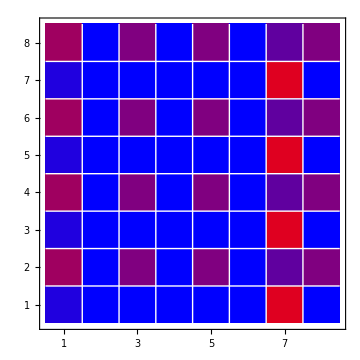
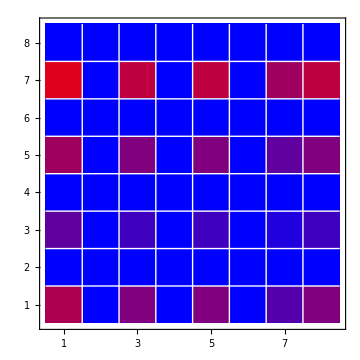
| Simulated Phase Behaviour of Surface Pulse | 
Sublattice A |  | Sublattice B
-Graphics- |  | -Graphics-

```mathematica
cells = Block[{reverseRange = Reverse[Range[8]]},
Table[{reverseRange[[i]],i},
{i,8}
]];
cells2 = Block[{range = Range[8]},Table[
{range[[i]],i},
{i,8}
]];

Grid[{{"",Text[Style["Simulated Phase Behaviour of Surface Pulse",FontSize->15]],""},{"Sublattice A","","Sublattice B"},{ArrayPlot[Transpose[coloredPulse][[;;,;;,1]],Mesh->{7,7},MeshStyle-> White,AspectRatio->1,Frame->True,FrameTicks->{cells,cells2},ImageSize->Medium]
,
BarLegend[{{RGBColor[1,0,0],RGBColor[0,0,1]},{0,2π}},LegendLayout->"Column",LegendLabel->"Phase of Node"]
,
ArrayPlot[Transpose[coloredPulse][[;;,;;,2]],Mesh->{7,7},MeshStyle-> White,AspectRatio->1,Frame->True,FrameTicks->{cells,cells2},ImageSize->Medium]}}]
```

```mathematica
ArrayPlot[Transpose[gradientPulse][[;;,;;,1]],Mesh->{7,7},MeshStyle-> White,AspectRatio->1,Frame->True,FrameTicks->{cells,cells2},ImageSize->Medium]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ArrayPlot::mat: Argument Transpose[Symbol[]] at position 1 is not a list of lists.

ArrayPlot[Transpose[Symbol[]],Mesh→{7,7},MeshStyle→GrayLevel[1],AspectRatio→1,Frame→True,FrameTicks→{{{8,1},{7,2},{6,3},{5,4},{4,5},{3,6},{2,7},{1,8}},{{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8}}},ImageSize→Medium]

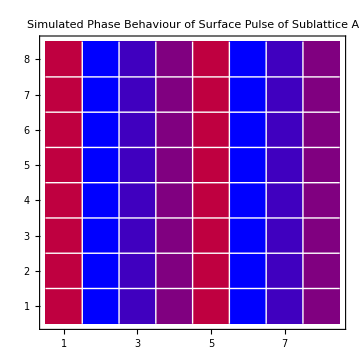

```mathematica
ArrayPlot[Transpose[coloredPulse][[;;,;;,1]],Mesh->{7,7},MeshStyle-> White,AspectRatio->1,Frame->True,FrameTicks->{cells,cells2},ImageSize->Medium,PlotLabel->Text[Style["Simulated Phase Behaviour of Surface Pulse of Sublattice A",FontSize->13]]]
```